```mathematica
Remove["Global`*"]
```

```mathematica
ResourceFunction["MaTeXInstall"][];
<<MaTeX`
texout={Frame->True,ImageSize->410,BaseStyle->Directive[FontSize->12],AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->12}};
```

```mathematica
F[α_,p_,ε_]:=
(α + p) ParabolicCylinderD[(ε-1)/2,p Sqrt[2]] -Sqrt[2] ParabolicCylinderD[(ε+1)/2,p Sqrt[2]]
```

```mathematica
contour=ContourPlot[
F[1,p,ε]==0, 
{p,-10,10},{ε,-1,9.01},
ColorFunction->Function[x,{0,0.5,0}]
]
```

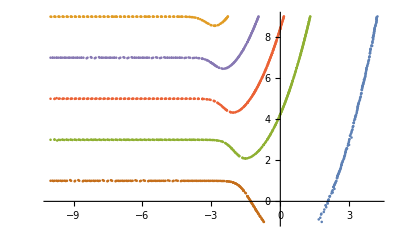

```mathematica
coord=Cases[Normal@contour,Line[x_]:>x,Infinity];
ListPlot[coord]
```

```mathematica
cfce[x_] := {
Piecewise[{ {1, x>0.5}, {0.6,x<0.5} , {0.6, x==0}}],
Piecewise[{ {0.6, x>0.5}, {0.6, x<0.5}, {0.6, x==0} }],
Piecewise[{ {0.6, x>0.5}, {1, x<0.5}, {0.6, x==0} }]
};
cfceBlend[x_] := Blend[RGBColor[cfce[#]] &/@ (Range[100]/100), x];
```

```mathematica
plot[α_]:=Show[
DensityPlot[2 LogisticSigmoid[ F[α,p,ε]]-1,{p,-10,10},{ε,-1,9.01},
ColorFunction->cfceBlend,
ClippingStyle->Automatic,
PlotLegends->None,
Evaluate@texout,
PlotLabel->MaTeX /@ {"\\alpha \\, \\sqrt{2b} = "<>ToString[a]},
FrameLabel->MaTeX/@{"p / \\sqrt{b}","\\epsilon / b"},
PerformanceGoal->"Quality"
],
ContourPlot[
F[α,p,ε]==0, 
{p,-10,10},{ε,-1,9.01},
ColorFunction->Function[x,{0,0.5,0}]
]
];
```

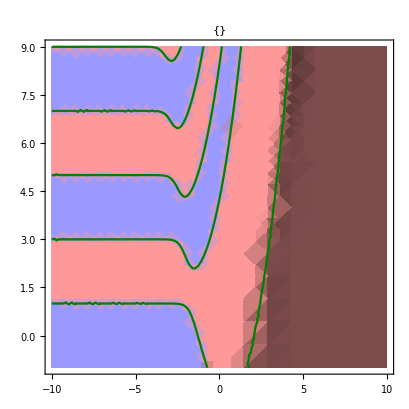

General::munfl: Exp[-5.31585×10^16] is too small to represent as a normalized machine number; precision may be lost.

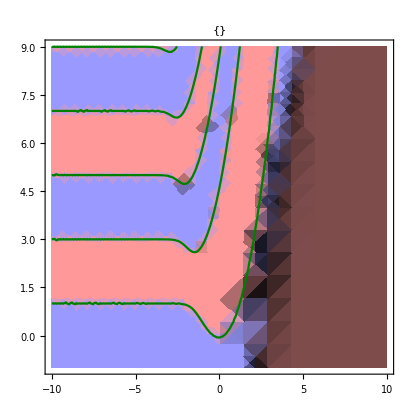

General::munfl: Exp[-5.51416×10^16] is too small to represent as a normalized machine number; precision may be lost.

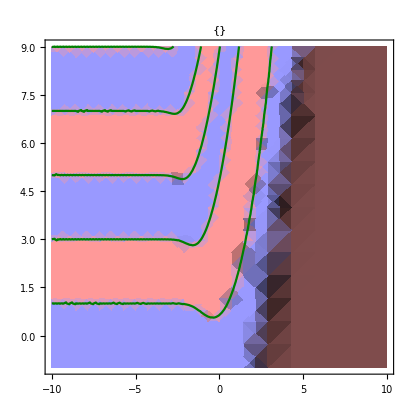

General::munfl: Exp[-5.58027×10^16] is too small to represent as a normalized machine number; precision may be lost.

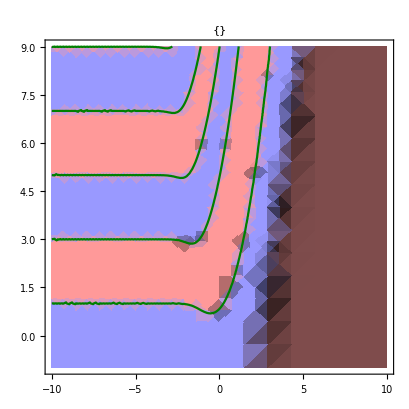

General::munfl: Exp[-5.63976×10^16] is too small to represent as a normalized machine number; precision may be lost.

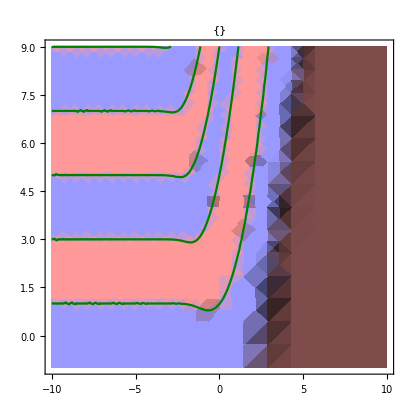

```mathematica
p = plot[1]
Export["robin1.pdf",p,ImageResolution->600];

p = plot[2]
Export["robin2.pdf",p,ImageResolution->600];

p = plot[5]
Export["robin5.pdf",p,ImageResolution->600];

p = plot[10]
Export["robin10.pdf",p,ImageResolution->600];

p = plot[100]
Export["robin100.pdf", p, ImageResolution->600];
```

```mathematica
plotContour[α_] := ContourPlot[
F[α,p,ε]==0, 
{p,-5,5},{ε,-5,10},
ColorFunction->Function[x,{0,0,0}],
Evaluate@texout,
PlotLabel->MaTeX /@ {"\\alpha / \\sqrt{b} = "<>ToString[α]},
FrameLabel->MaTeX/@{"p / \\sqrt{b}","\\epsilon / b"},
PerformanceGoal->"Quality",
WorkingPrecision->200,
MaxRecursion -> 2
];
```

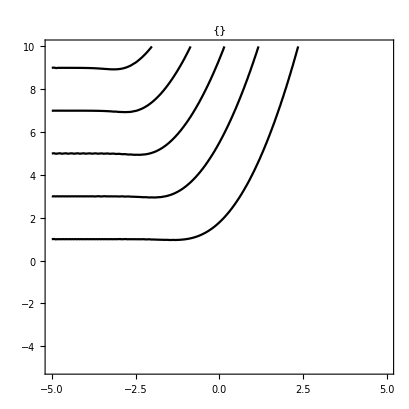

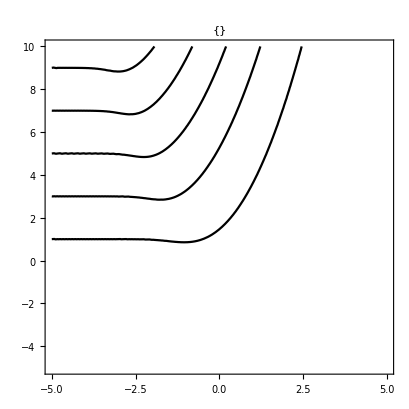

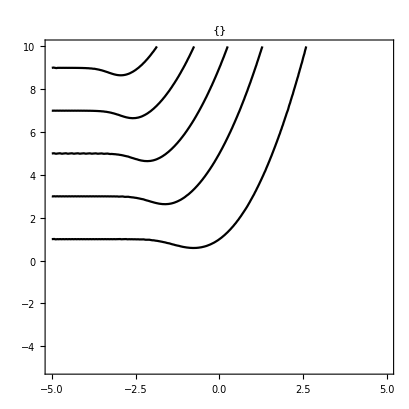

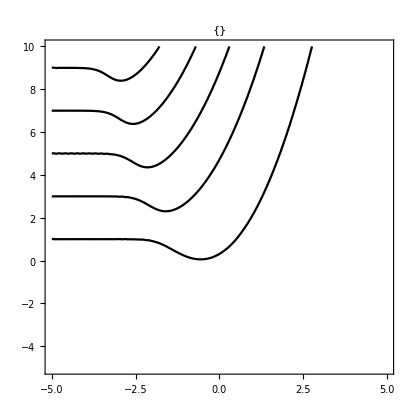

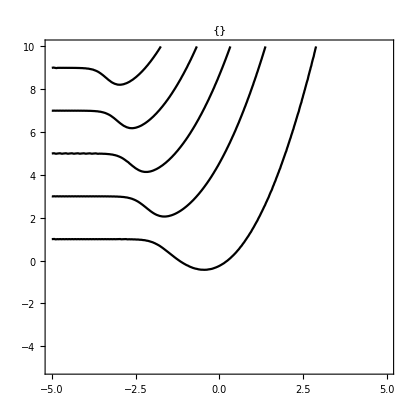

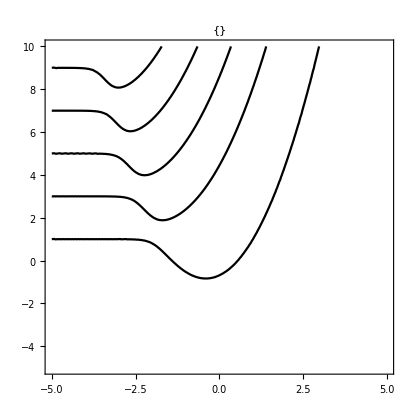

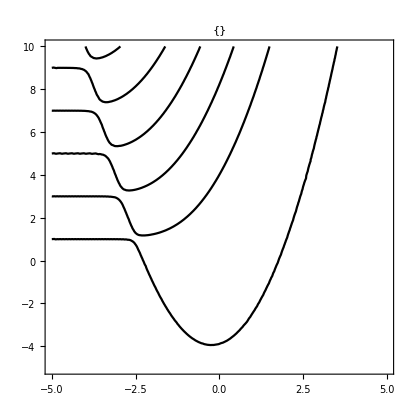

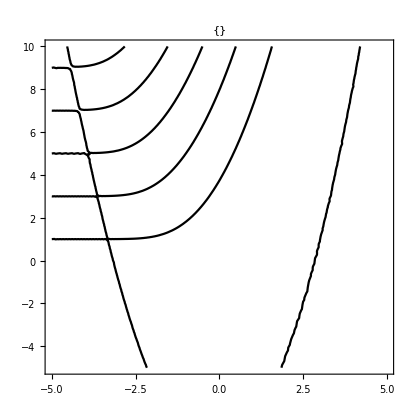

```mathematica
p = plotContour[-1]
Export["robin-1.pdf",p,ImageResolution->600];

p = plotContour[-0.5]
Export["robin-0.5.pdf",p,ImageResolution->600];

p = plotContour[0]
Export["robin0.pdf",p,ImageResolution->600];

p = plotContour[0.5]
Export["robin0.5.pdf",p,ImageResolution->600];

p = plotContour[0.8]
Export["robin0.8.pdf",p,ImageResolution->600];

p = plotContour[1]
Export["robin1.pdf",p,ImageResolution->600];

p = plotContour[2]
Export["robin2.pdf",p,ImageResolution->600];

p = plotContour[3]
Export["robin5.pdf",p,ImageResolution->600];

p = plotContour[4]
Export["robin5.pdf",p,ImageResolution->600];
```

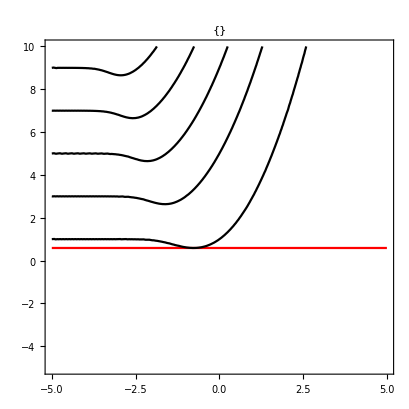

```mathematica
p = Show[
ContourPlot[
ε == 0.590106125,
{p,-5,5},{ε,-5,10},
ContourStyle->{Red},
Evaluate@texout,
PlotLabel->MaTeX /@ {"\\alpha / \\sqrt{b} = 0"},
FrameLabel->MaTeX/@{"p / \\sqrt{b}","\\epsilon / b"}
],
ContourPlot[
F[0,p,ε]==0, 
{p,-5,5},{ε,-5,10},
ColorFunction->Function[x,{0,0,0}],
Evaluate@texout,
PlotLabel->MaTeX /@ {"\\alpha / \\sqrt{b} = 0"},
FrameLabel->MaTeX/@{"p / \\sqrt{b}","\\epsilon / b"},
PerformanceGoal->"Quality",
WorkingPrecision->200,
MaxRecursion -> 2
]
]

Export["robin0-degennes.pdf",p,ImageResolution->600];
```

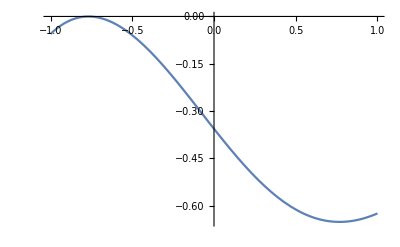

```mathematica
Plot[F[0,p,0.59],{p,-1,1}]
```

```mathematica
;
```

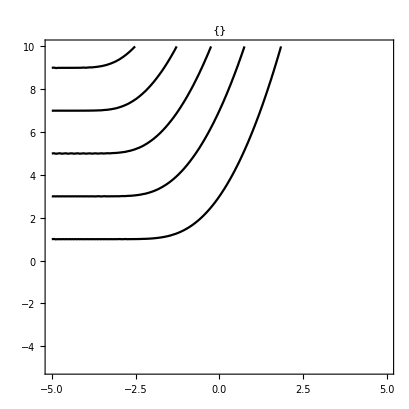

```mathematica
p = ContourPlot[
ParabolicCylinderD[(ε-1)/2,p Sqrt[2]]==0, 
{p,-5,5},{ε,-5,10},
ColorFunction->Function[x,{0,0,0}],
Evaluate@texout,
PlotLabel->MaTeX /@ {"\\alpha / \\sqrt{b} = -\\infty"},
FrameLabel->MaTeX/@{"p / \\sqrt{b}","\\epsilon / b"},
PerformanceGoal->"Quality",
WorkingPrecision->200,
MaxRecursion -> 2
]


Export["dirichlet.pdf",p,ImageResolution->600];
```